```mathematica
repZero2
```

{v1x2x3x4x5→0,v1x24x35→0,v14x2x35→0,v14x25x3→0,v13x25x4→0,v13x24x5→0}

```mathematica
Select[Sort[Tally[Table[allGraphs[k,"colofour"]/.repZero2,{k,Keys[allGraphs]}]],#1[[2]]>#2[[2]]&],Length[ListofVars[#[[1]]]]==1&]
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

{{v13x2x4x5,5},{v14x2x3x5,5},{v1x24x3x5,5},{v1x25x3x4,5},{v1x2x35x4,5},{v124x35,3},{v134x25,3},{v135x24,3},{v13x245,3},{v14x235,3},{v1234x5,2},{v1235x4,2},{v1245x3,2},{v12x3x4x5,2},{v1345x2,2},{v15x2x3x4,2},{v1x2345,2},{v1x23x4x5,2},{v1x2x34x5,2},{v1x2x3x45,2},{v12345,1},{v123x45,1},{v123x4x5,1},{v124x3x5,1},{v125x34,1},{v125x3x4,1},{v12x345,1},{v12x34x5,1},{v12x35x4,1},{v12x3x45,1},{v134x2x5,1},{v135x2x4,1},{v13x2x45,1},{v145x23,1},{v145x2x3,1},{v14x23x5,1},{v15x234,1},{v15x23x4,1},{v15x24x3,1},{v15x2x34,1},{v1x234x5,1},{v1x235x4,1},{v1x23x45,1},{v1x245x3,1},{v1x25x34,1},{v1x2x345,1}}

```mathematica
same=Select[Keys[allGraphs],(allGraphs[#,"colofour"]/.repZero2)==v14x2x3x5&]
```

{31681,31708,31711,31684,27337}

```mathematica
reptext=Table[stubbornForm5[k,"colofour"]->Labeled[Graph[allGraphs[k,"graph"],ImageSize->{40,40}],Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k],If[MemberQ[{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key},k],{FontFamily->"Consolas", Italic,Bold,Underlined},Plain]]],{k,baseKeys5}];
```

```mathematica
Table[ChromaticPolynomial[allGraphs[k,"graph"],4]/24//Factor,{k,same}]//TableForm
```

3
2
1
2
1

```mathematica
def=Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"],sets=allGraphs[#,"vertexsets"]},VertexCount[g]==4&& EdgeCount[g]==5&&MemberQ[sets,{1,4}]]&]
```

{31708,31684,31468,30981,25141,11947}

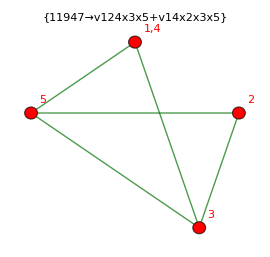
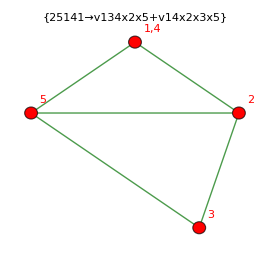
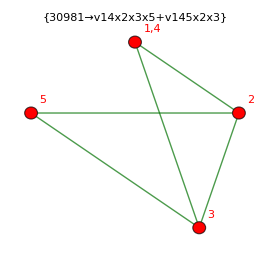
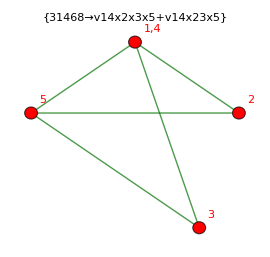
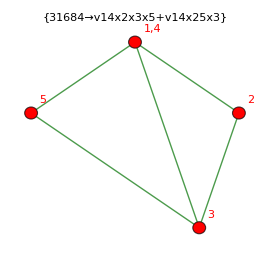
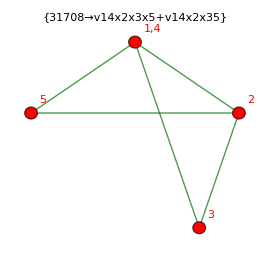

```mathematica
Sort[Table[Graph[allGraphs[k,"graph"],PlotLabel->{k->allGraphs[k,"colofour"]/.reptext},ImageSize->270]/.repZero2,{k,def}],If[VertexCount[#1]==VertexCount[#2],
	EdgeCount[#1]<EdgeCount[#2],
VertexCount[#1]<VertexCount[#2]
]&]
```

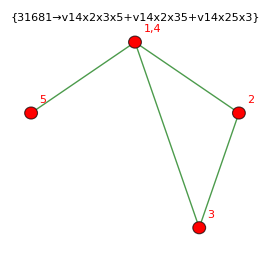
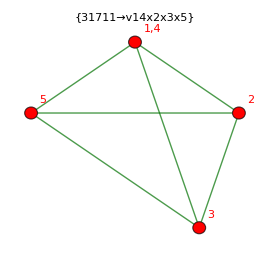
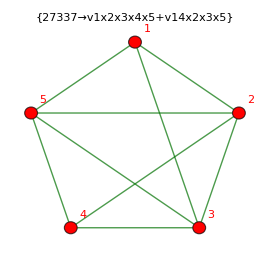
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sort[Table[Graph[allGraphs[k,"graph"],PlotLabel->{k->allGraphs[k,"colofour"]/.reptext},ImageSize->270]/.repZero2,{k,same}],If[VertexCount[#1]==VertexCount[#2],
	EdgeCount[#1]<EdgeCount[#2],
VertexCount[#1]<VertexCount[#2]
]&]
```